```mathematica
Quit[]
```

```mathematica
<<MaTeX`
```

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"];
```

```mathematica
Clear["Global`*"]
```

## Initial Conditions in Radiation

### System

#### Variables

The dynamical variables are

.00.10.00.00.00.00.00.00.08.00.00.00.00.00.00.00(.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00\[CapitalIAcute].00.00.00.02.00.00.00\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00&.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00032\[DownQuestion]\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalIAcute].00.00.00\[CapitalUGrave]#.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOHat].02<,\[CapitalATilde].02.00.00\[CapitalEth].00.00.00.00.00.00.00\[CapitalAGrave].0c<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.08'.9c.81\[Divide].82.00.00032\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00
qc.bc\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.10.00.00.00.00.00.00.9e.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\[CapitalOSlash].80\[ODoubleDot]\\[Divide].7f.00.00.00.10.00.00.00.00.00.00N5\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\[Eth]#.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.897\[CapitalATilde].02.00.00 R.880\[CapitalATilde].02.00.00!X.9f.bc\[YDoubleDot].7f.00.00.00.10.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.0e.00.00\[CapitalAGrave].00.00.00.00.00.00.00.00.00.00.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00Lc.9f.bc\[YDoubleDot].7f.00.00\[OSlash]R.880\[CapitalATilde].02.00.00 R.880\[CapitalATilde].02.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[OSlash]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.9e.00.00.00.00.00.00.00\[LeftGuillemet]U.9f.bc\[YDoubleDot].7f.00.00 R.880\[CapitalATilde].02.00.00.9e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEGrave].04.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00@\[CapitalEth].9c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.90%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]T.9f.bc\[YDoubleDot].7f.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[RightGuillemet]y.9f.bc\[YDoubleDot].7f.00.00 R.880\[CapitalATilde].02.00.00.9e.00.00.00.00.00.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00
.00.00.00.00.00.00.00.80%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00FT.9f.bc\[YDoubleDot].7f.00.00.90%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00y%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.9e.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.000C\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[CapitalIGrave]S.9f.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00@m.9f.bc\[YDoubleDot].7f.00.00\[CapitalAGrave]\[NTilde].870\[CapitalATilde].02.00.00.80%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DownQuestion].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.06.00.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[Eth].1510\[CapitalATilde].02.00.00.10\[CapitalEth]\[CapitalEth]Y\[CapitalATilde].02.00.00.11.85\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.10=Y,\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00\[NTilde].870\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 R.880\[CapitalATilde].02.00.007.87\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[Degree].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[EDoubleDot]7\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.14L\[ODoubleDot]\\[Divide].7f.00.00 R.880\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]G\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00(\[RightGuillemet]\[YDoubleDot]\\[Divide].7f.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01{\[CapitalAHat]x\[CapitalATilde].02.00.00.00.02.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CapitalAHat]x\[CapitalATilde].02.00.00.00.9d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree]G\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[OSlash].9c.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.07.00.00.00.00.00.00.00.80.98.92X\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]O.92x\[CapitalATilde].02.00.00.07.00.00.00.00.00.00.00T.81\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[OSlash].94.s\[CapitalATilde].02.00.00 |\[CapitalAHat]x\[CapitalATilde].02.00.00\[Eth]{\[CapitalAHat]x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[AGrave]{\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00`(.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00\[CapitalEth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]\[UDoubleDot]g.ba\[YDoubleDot].7f.00.00 .82\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00 .82\[CapitalAHat]x\[CapitalATilde].02.00.00\[OHat]\[Yen]u.be\[YDoubleDot].7f.00.00O.8cbD\[RightGuillemet]cq.04\[CapitalEth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 |\[CapitalAHat]x\[CapitalATilde].02.00.00\[Eth]{\[CapitalAHat]x\[CapitalATilde].02.00.00 .19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Yen]$.0f.bd\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00 ).7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 .19.8eO\[CapitalATilde].02.00.00\[NonBreakingSpace].00.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.008.88e.ba\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00 ).7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00p.19.8eO\[CapitalATilde].02.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalAHat]&\[Times]Y\[CapitalATilde].02.00.00B\[Cedilla]g.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00C.00:.00\.00W.00I.00N.00D.00O.00W.00S.00\.00F.00o.00n.00t.00s.00.00.00e.00D.00r.00i.00v.00e.00\.00D.00o.00c.00u.00m.00e.00n.00t.00o.00s.00.00.00o.00s.00o.00f.00t.00\.00W.00i.00n.00d.00o.00w.00s.00\.00R.00e.00c.00e.00n.00t.00.00.00e.00n.00u.00.00.00yTu.be\[YDoubleDot].7f.00.00.00.00W,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.90.03<,\[CapitalATilde].02.00.00\[CapitalAGrave].03.00.00.00.00.00.00.02.00.00.00.00.00.00.00.15Kr.be\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave].81.9c.be\[YDoubleDot].7f.00.00.08.00.00.00.00.00.00.00\[CapitalAGrave].03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]*.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.03.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.10,.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00N\[AE]j.be\[YDoubleDot].7f.00.001HO.00.00.00.00.00(.19.8eO\[CapitalATilde].02.00.00.10+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Yen]\[YAcute]e.ba\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalAHat]x.99\[CapitalODoubleDot].90.15.00.00.03.00.00.00.00.00.00.00\[OGrave]x.99\[CapitalODoubleDot].90.15.00.00.00.00.00.00.00.00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.10,.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.afkl.ba\[YDoubleDot].7f.00.00h+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00B.02.10.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.b2.8bs.be\[YDoubleDot].7f.00.00.00.19.8eO.00.00.00.00x.8e.9bx\[CapitalATilde].02.00.00%.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.000.8e.9bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00\[Eth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.84P.88.bc\[YDoubleDot].7f.00.00.18.00.00.00.00.00.00.00\[CapitalOGrave].9e1\[DownQuestion]\[YDoubleDot].7f.00.00fzH\[CapitalThorn]1.7f.00.00\[AGrave].00.00.00.00.00.00.00.8a.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00f\[NTilde]/\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace]/.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.02.00.00.00.00.00.00.00(.00.00.00.00.00.00.00\[Eth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[ADoubleDot]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000.8e.9bx\[CapitalATilde].02.00.00.00.00.00.00.04.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.04.00.00.00C.00:.00\.00U.00s.00e.00r.00s.00\.00s.00a.00n.00v.00x.00.00.00.00.00@k@\[DownQuestion]\[YDoubleDot].7f.00.00o.00a.00d.00s.00\.00d.00e.00s.00k.00t.00o.00p.00..00i.00n.00i.00.00.000\[DownQuestion]\[YDoubleDot].7f.00.00I.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01E.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00`.00.00.00.00.00.00.00P\[CapitalUDoubleDot]\[Paragraph]I\[CapitalATilde].02.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00@w<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00p.aa\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[Cedilla].02<,\[CapitalATilde].02.00.00`.00.00.00.00.00.00.00.00
<,.00.00.00.00L^.92x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00|.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot].7f.00.00.90-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.84P.88.bc\[YDoubleDot].7f.00.00.08.00.00.00.00.00.00.00\[Thorn]\[YDoubleDot]\[YDoubleDot].7f.00.00.00.00\[CapitalIHat].02.00.00.00.00.00.00\[ODoubleDot].00.00.00.00.00.00.00r0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.;c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.80-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.16.00.00.00.00.00.00.00.90-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10.00.00.00.00.00.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00C.00:.00\.00U.00s.00e.00r.00s.00C.00:.00\.00U.00s.00e.00r.00s.00\.00s.00a.00n.00t.00i.00.00.00.00.007.00-.00F.000.007.007.00-.004.00.00.00.00.00.00.00.00.00J.00.00.00.00.00.00.00.900.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.900.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.8d\[CapitalOSlash]b.bc\[YDoubleDot].7f.00.00!.90.88\[CapitalUHat].81{.00.00.08.00.00.00.00.00.00.00(.00.00.00.00.00.00.00\[Degree].98\[CapitalAHat]x\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01+\[Times]Y\[CapitalATilde].02.00.00.88.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00%.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.8e.9bx\[CapitalATilde].02.00.00.05.00.00.00.00.00.00.00.00.b4~_\[CapitalATilde].02.00.00.17\[UHat]b.bc\[YDoubleDot].7f.00.00@.00.00.00\[YDoubleDot].7f.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00A.02.bc.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00B.02#.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.88.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalIAcute].00.00.00.80C<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.80.<,\[CapitalATilde].02.00.00\[Degree].02<,\[CapitalATilde].02.00.00@.00.00.00.00.00.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00,.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00.98/.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.9c\[UHat]c.bc\[YDoubleDot].7f.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.00.00\[CapitalATilde].02.00.00.02.00.00.00\[YDoubleDot].7f.00.00 .00.00.00.00.00.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.0c.00.00.00\[CapitalATilde].02.00.00A8c.bc\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00p0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Currency]\[Degree]W\[CapitalIDoubleDot]"p\[CapitalUAcute].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[PlusMinus].94.88\[CapitalUHat].81{.00.00\[CapitalNTilde].96.88\[CapitalUHat].81{.00.00h.be*O\[CapitalATilde].02.00.00\[CapitalAAcute].96.88\[CapitalUHat].81{.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00h.be*O\[CapitalATilde].02.00.00(G.s\[CapitalATilde].02.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00p0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00A8c.bc\[YDoubleDot].7f.00.00.10.00.00.00.00.00.00.00\[CapitalIDoubleDot]"k.ba\[YDoubleDot].7f.00.00(G.s\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00.008\[DiscretionaryHyphen]g.ba\[YDoubleDot].7f.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00p,\[Times]Y.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00x.96.s\[CapitalATilde].02.00.00s.00a.00n.00t.00i.00.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.18q.be.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.004\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00,.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[IHat])\[Times]Y\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00\[EGrave]1.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.9c\[UHat]c.bc\[YDoubleDot].7f.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.00.00\[CapitalATilde].02.00.00.02.00.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.1d.00.00.00.00.00\[AGrave].00.00.00.00.00.00.000\[CapitalThorn].b9I\[CapitalATilde].02.00.00\[CapitalAGrave]2.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[IGrave]RU\[CapitalIDoubleDot]"p\[CapitalUAcute].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.05.00.0f.00.00.00.00.00\[AGrave].00.00.00.00.00.00.000\[CapitalThorn].b9I\[CapitalATilde].02.00.00 
<,\[CapitalATilde].02.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00@7=,\[CapitalATilde].02.00.00.18.af\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0093.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]+\[Times]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00/^.92x\[CapitalATilde].02.00.00\[Not].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00\[CapitalATilde].02.00.00\[CapitalEGrave]@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00`\[OGrave].91x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]4.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.98x.80WO.8cbD\[RightGuillemet]cq.04#.80\[PlusMinus]	.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00p\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00\[IDoubleDot].be.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00 ^.92x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[NonBreakingSpace]4.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[EGrave].95.s\[CapitalATilde].02.00.00\[OSlash]ng.ba\[YDoubleDot].7f.00.00p\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.b4~_\[CapitalATilde].02.00.00.00.10.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.05.00.10.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[NonBreakingSpace].b2\[UAcute]U\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.04.00
.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[NonBreakingSpace].b2\[UAcute]U\[CapitalATilde].02.00.00S#u.be\[YDoubleDot].7f.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00@7=,\[CapitalATilde].02.00.00.18.af\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00-.00.00.00.00.00.00.00\[Cent].00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[Cedilla]@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00\[Degree]b.92x\[CapitalATilde].02.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.006zf.ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]E.s\[CapitalATilde].02.00.00\[CapitalOSlash]?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOSlash]?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.16xf.ba\[YDoubleDot].7f.00.0006.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[Eth]E.s\[CapitalATilde].02.00.00F\[IAcute]X.ba\[YDoubleDot].7f.00.00.18C.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00`\[OGrave].91x\[CapitalATilde].02.00.00.12:..bd\[YDoubleDot].7f.00.00@7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[Eth]6.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.98x.80W.03.03bD\[RightGuillemet]cq.04.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.000*\[Times]Y\[CapitalATilde].02.00.00.02.02.00.00\[CapitalATilde].02.00.00\[Degree]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Cedilla]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Cedilla]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00
.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00.90\[Sterling][7\[CapitalATilde].02.00.00\[Degree]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00b\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00B\[Cedilla]g.ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00W.00\[IGrave].02.00.00.00.00 .00.00.00.00.00.00.00.00/17\[CapitalATilde].02.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalEth]8.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00P.00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00.00$<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[DoubleDot].02<,\[CapitalATilde].02.00.00 .00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.197.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.b4.02<,\[CapitalATilde].02.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Y7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.18.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00C.02.1e.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00<.04.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalOGrave].3\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00.80.<,\[CapitalATilde].02.00.00\[CapitalEth]+\[Times]Y\[CapitalATilde].02.00.00\[OSlash]\[Thorn]/\[DownQuestion]\[YDoubleDot].7f.00.00.80.8b\[CapitalOSlash].ba\[YDoubleDot].7f.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00F.02.85.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00@.00.00.00.00.00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00.1e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80C<,\[CapitalATilde].02.00.00`:.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00I8.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree].02<,\[CapitalATilde].02.00.00@.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.02.00.00.00\[YDoubleDot].7f.00.00.00.00.00.0b.05.02.00.00.00.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright]8.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00\[CapitalATilde].02.00.000.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalThorn]X.ba\[YDoubleDot].7f.00.00.02.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.15.00.00.00.00.00\[AGrave].00.00.00.00.00.00.000\[CapitalThorn].b9I\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00@<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOSlash]\[Paragraph]\[CapitalODoubleDot]r\[CapitalATilde].02.00.00\[OSlash].94.s\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].96.s\[CapitalATilde].02.00.00.1e.00.00.00.00.00.00.00h3.9c.81\[Divide].82.00.00.1e3h.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00P.81\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[OSlash].94.s\[CapitalATilde].02.00.00p.98\[CapitalAHat]x\[CapitalATilde].02.00.00@<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.80.8b\[CapitalOSlash].ba\[YDoubleDot].7f.00.00@:.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00;6k.ba\[YDoubleDot].7f.00.00.90.15\[Thorn]7\[CapitalATilde].02.00.00\[NonBreakingSpace]\[CapitalEAcute]g.ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00.05.00.00.00.00.00.00.00`:.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00 .80.<,\[CapitalATilde].02.00.000<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00@.beX,\[CapitalATilde].02.00.00\[Currency].02<,\[CapitalATilde].02.00.00".00.00.00.00.00.00.00.08.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000@.00.00\[CapitalIAcute].00.00.00G/.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00\[CapitalATilde].02.00.00.00.00.00.02.00.00.00.00.00.00<,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00".00.00.00.00.00.00.00.08.00.00.00.91
\[Cedilla]\[Thorn]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.80.8b\[CapitalOSlash].ba\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalIAcute].00.00.00@<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[IDoubleDot]].92x\[CapitalATilde].02.00.00\[LeftGuillemet].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00\[YDoubleDot].7f.00.00H<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.80\[CapitalAHat]\[CapitalOSlash].ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00.00.00.00.0b.05.02.00.00.00.00.00.00.00.00.00.00@;.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.91f\[CapitalEDoubleDot].ba\[YDoubleDot].7f.00.007.00.00.00.02.00.00.00.02v\[CapitalEHat].ba\[YDoubleDot].7f.00.00G.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalOSlash]9.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.00.00.00.00.00.00.00\[CapitalAGrave]9.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.04.00.00.00.00.00.00.00\[CapitalEGrave]9.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.04.00.00.00.00.00.00.00\[CapitalOGrave]i.99\[CapitalODoubleDot].90.15.00.00.00.00W,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00@<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]].92x\[CapitalATilde].02.00.00.11.00.00.00.00.00.00.00.af.97\[CapitalAHat]x\[CapitalATilde].02.00.00.1e.03.00.00.00.00.00.00\[NonBreakingSpace].95\[CapitalAHat]x\[CapitalATilde].02.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00 .01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CapitalAHat]x\[CapitalATilde].02.00.00\[CapitalEHat]\[YDoubleDot]g.ba\[YDoubleDot].7f.00.00.00.00.00.0b.05.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00`;.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.007.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00\[Eth]].92x\[CapitalATilde].02.00.00.07.00.00.00.00.00.00.00T.81\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[OSlash].94.s\[CapitalATilde].02.00.00p.98\[CapitalAHat]x\[CapitalATilde].02.00.00\[Degree].97\[CapitalAHat]x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace].97\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[CapitalEth]<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00@@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]\[UDoubleDot]g.ba\[YDoubleDot].7f.00.00\[NonBreakingSpace].95\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00<.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000.00.00.00.00.00.00.00\[NonBreakingSpace].95\[CapitalAHat]x\[CapitalATilde].02.00.00\[OHat]\[Yen]u.be\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00@@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p.98\[CapitalAHat]x\[CapitalATilde].02.00.00\[Degree].97\[CapitalAHat]x\[CapitalATilde].02.00.00 \[Degree]\[OAcute]B\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00HE.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Yen]$.0f.bd\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00.90=.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 \[Degree]\[OAcute]B\[CapitalATilde].02.00.00\[CapitalAGrave].b2\[OAcute]B\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.008.88e.ba\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00.90=.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00p\[Degree]\[OAcute]B\[CapitalATilde].02.00.00p\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.00.00.00.00.02.00.00.00p\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00b\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00B\[Cedilla]g.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00C.00:.00\.00W.00I.00N.00D.00O.00W.00S.00\.00F.00o.00n.00t.00s.00.00.00e.00D.00r.00i.00v.00e.00\.00D.00o.00c.00u.00m.00e.00n.00t.00o.00s.00.00.00o.00s.00o.00f.00t.00\.00W.00i.00n.00d.00o.00w.00s.00\.00R.00e.00c.00e.00n.00t.00.00.00e.00n.00u.00.00.00yTu.be\[YDoubleDot].7f.00.00.00.00W,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.90.03<,\[CapitalATilde].02.00.00\[CapitalAGrave].03.00.00.00.00.00.00.02.00.00.00.00.00.00.00.15Kr.be\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave].81.9c.be\[YDoubleDot].7f.00.00.08.00.00.00.00.00.00.00\[CapitalAGrave].03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.009?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.03.00.00.00.00.00.00.00HE.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.80@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00N\[AE]j.be\[YDoubleDot].7f.00.001HO.00.00.00.00.00(\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.80?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalATilde].02.00.00.02.00.00.00\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00Rl.99\[CapitalODoubleDot].90.15.00.00.03.00.00.00.00.00.00.00Bl.99\[CapitalODoubleDot].90.15.00.00.00.00.00.00.00.00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00HE.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00HE.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.03.00.00.00.00.00.00.00.80@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.afkl.ba\[YDoubleDot].7f.00.00\[CapitalOSlash]?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00\[IDoubleDot].be.00.00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00 \[Degree]\[OAcute]B\[CapitalATilde].02.00.00(\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.b2.8bs.be\[YDoubleDot].7f.00.00(\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.80@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.03.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00i@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[ARing].00.00.00\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00 \[Degree]\[OAcute]B\[CapitalATilde].02.00.00\[DoubleDot]\[Degree]\[OAcute]B\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[AGrave].7f.9c.be\[YDoubleDot].7f.00.00x,.95.be\[YDoubleDot].7f.00.00\[AAcute]\[UHat]\[CapitalEAcute].9a\[Cent]\[AGrave]\[CapitalODoubleDot]J.b4\[IHat]\[AHat].12.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01>\[Copyright].17.00.00.00.00.00.00.00.00MEOW.04.00.00.00.1em.82C.18\[CCedilla]\[IHat]B.bcU\[DownExclamation]\[AHat]a\[CapitalATilde]{\[Thorn]\[AAcute]\[UHat]\[CapitalEAcute].9a\[Cent]\[AGrave]\[CapitalODoubleDot]J.b4\[IHat]\[AHat].12.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01>\[Copyright].17.00.00.00.00\[ARing].00.00.00x,.95.be\[YDoubleDot].7f.00.00\[Cedilla]A.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000D.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Sterling]\[SZ]\[IGrave].be\[YDoubleDot].7f.00.00x,.95.be\[YDoubleDot].7f.00.00x,.95.be\[YDoubleDot].7f.00.00\[CapitalIGrave]\[CapitalEHat]\[DownQuestion].a6\[Not] .00.00XF.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00HE.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00(\[Degree]\[OAcute]B\[CapitalATilde].02.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave]A.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00fas.be\[YDoubleDot].7f.00.00.02.00.00.00.00.00.00.00\[AGrave]A.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00(\[Degree]\[OAcute]B\[CapitalATilde].02.00.00kUv.be\[YDoubleDot].7f.00.00.03.00.00.00.00.00.00.00.80A.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00@\[Yen]k.be\[YDoubleDot].7f.00.00 )\[ODoubleDot]W\[CapitalATilde].02.00.00,.8aq.be\[YDoubleDot].7f.00.00 )\[ODoubleDot]W\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalAGrave]\[CCedilla].90.be\[YDoubleDot].7f.00.00.98\[CCedilla].90.be\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 )\[ODoubleDot]W\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Yen]\[YAcute]e.ba\[YDoubleDot].7f.00.00#.03.00.00.00.00.00.00\[CapitalAGrave].00.00.00.00.00.00F.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00+.00
.00.00.00.00.00.10.02.00.00.00.00.00.00\[CapitalEth]\[CapitalThorn].98^\[CapitalATilde].02.00.00\[CapitalAGrave].00.00.00.00.00.00F.00.00.00.00.00.00.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalAGrave]\[ADoubleDot]<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00O.02\[Yen].02.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AE].8cK3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.98J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00pD.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace].81\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]D.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00\[CapitalEDoubleDot].a6\[CapitalEth].9d\[YDoubleDot].7f.00.00pJ.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00<nf3\[CapitalATilde].02.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.04.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\.00s.00a.00n.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[OHat]nf3\[CapitalATilde].02.00.00o.00a.00d.00s.00.18\[UHat].1c3\[CapitalATilde].02.00.00k.00t.00o.00p.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.000\[DownQuestion]\[YDoubleDot].7f.00.00O.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01W.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00`.00.00.00.00.00.00.00jxf3\[CapitalATilde].02.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00>xf3\[CapitalATilde].02.00.00.04.00c.bc\[YDoubleDot].7f.00.00lxf3\[CapitalATilde].02.00.00.04.00<,\[CapitalATilde].02.00.00>xf3\[CapitalATilde].02.00.00.00.00\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00>xf3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[CapitalIAcute].00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[YDoubleDot].7f.00.00`J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.84N.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00pJ.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.1cG.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000F.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.85.13\[CapitalEth].9d\[YDoubleDot].7f.00.00\[AE].8cK3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.88L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`F.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace].81\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90F.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00\[CapitalEDoubleDot].a6\[CapitalEth].9d\[YDoubleDot].7f.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00PL.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00<nf3\[CapitalATilde].02.00.00PN.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[OHat]nf3\[CapitalATilde].02.00.00 G.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.05.00.00.00.00.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00?\[LeftGuillemet]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00 J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00GPOS.00.00.00.00.96xf3\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00>xf3\[CapitalATilde].02.00.00.04.00\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.00.98xf3\[CapitalATilde].02.00.00.04.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AE].8cK3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[CapitalIAcute].00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[YDoubleDot].7f.00.00PL.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00tP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.0cI.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 H.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.85.13\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00f3\[CapitalATilde].02.00.00j.85g3\[CapitalATilde].02.00.00PN.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.00g3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00tP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00PL.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.15.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.0cI.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.8e.10\[CapitalEth].9d\[YDoubleDot].7f.00.00.04.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[IHat]D\[CapitalEth].9d\[YDoubleDot].7f.00.00.02.00.00.00.00.00.00.00	.00\[CapitalIGrave].9d\[YDoubleDot].7f.00.00.90L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.008L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[UGrave]\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.008L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00<nf3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00r.9d\[CapitalYAcute].bc\[YDoubleDot].7f.00.00(I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.05.00.00.00.00.00.00.00PN.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00?\[LeftGuillemet]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00.10L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00GPOS.00.00.00.00N.04f3\[CapitalATilde].02.00.00.15.00.00.00.00.00.00.00.80I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Sterling]\[UDoubleDot]\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.00.87.00.00.00.00.00.00.00.90L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00I.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalAGrave]I.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]H.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[OHat]H.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00tP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00PL.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.15.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.0cI.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.06.00.00.00.15.00.00.00.00L.7f\[CapitalUDoubleDot]J.00.00.00\[AE].8cK3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00XP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace].81\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`J.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00\[CapitalEDoubleDot].a6\[CapitalEth].9d\[YDoubleDot].7f.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00<nf3\[CapitalATilde].02.00.00 R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.05.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.98N.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[OHat]nf3\[CapitalATilde].02.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[CapitalThorn]cK3\[CapitalATilde].02.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00`L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00tP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01f3\[CapitalATilde].02.00.00.96xf3\[CapitalATilde].02.00.00.98N.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00.04.00	.11.11.00.00.00.98xf3\[CapitalATilde].02.00.00.04.00.00.00.00.00.00.00>xf3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AE].8cK3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[CapitalIAcute].00.00.00.04.00.06.00.08.00
.00.0c.00.0e.00\[YDoubleDot].7f.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00DT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalUDoubleDot]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]K.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.85.13\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00f3\[CapitalATilde].02.00.00j.85g3\[CapitalATilde].02.00.00 R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.00g3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00DT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.15.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalUDoubleDot]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.8e.10\[CapitalEth].9d\[YDoubleDot].7f.00.00.04.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[IHat]D\[CapitalEth].9d\[YDoubleDot].7f.00.00.02.00.00.00.00.00.00.00	.00\[CapitalIGrave].9d\[YDoubleDot].7f.00.00`P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave]O.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[OSlash]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[UGrave]\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.00.08P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00<nf3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00r.9d\[CapitalYAcute].bc\[YDoubleDot].7f.00.00\[OSlash]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOSlash]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.05.00.00.00.00.00.00.00 R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00?\[LeftGuillemet]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00\[AGrave]O.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00GPOS.00.00.00.00N.04f3\[CapitalATilde].02.00.00.15.00.00.00.00.00.00.00PM.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Sterling]\[UDoubleDot]\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.00.87.00.00.00.00.00.00.00`P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00I.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave]O.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90M.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalAGrave]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalADoubleDot]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00DT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.15.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalUDoubleDot]L.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.06.00.00.00.15.00.00.00.00P.7f\[CapitalUDoubleDot]J.00.00.00I.00.00.00.87.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.15.00.7f\[CapitalUDoubleDot].87.00.00.00GPOS\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00 R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalAHat].05f3\[CapitalATilde].02.00.00.05.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00*\[YDoubleDot].1c3\[CapitalATilde].02.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.02.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00d.00.00.00.83.00.00.00.98\[CapitalADoubleDot]40\[CapitalATilde].02.00.00\[AGrave]\[CapitalATilde]40\[CapitalATilde].02.00.00.15.00.15.00\[CapitalATilde].02.00.00.b4}80\[CapitalATilde].02.00.00\[AGrave]O.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00N.04f3\[CapitalATilde].02.00.00pP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00hP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[UHat].1c3\[CapitalATilde].02.00.00\[EHat].00f3\[CapitalATilde].02.00.00.05.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01f3\[CapitalATilde].02.00.004ZK3\[CapitalATilde].02.00.00hR.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00 N.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalThorn]cK3\[CapitalATilde].02.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00DT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01f3\[CapitalATilde].02.00.004ZK3\[CapitalATilde].02.00.00hR.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00			.05					.11.11.00.00.00.00.00	.00.00.00.11.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEHat]\[DoubleDot]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalIDoubleDot]\[Yen]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.12.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[DoubleDot]\[Not]\[CapitalIGrave].9d\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[EHat].ba\[CapitalIDoubleDot].9d\[YDoubleDot].7f.00.00DFLT.00.00.00.00r.9d\[CapitalYAcute].bc\[YDoubleDot].7f.00.00.10`80\[CapitalATilde].02.00.00R..00.00.00.00.00.00.00.00.00.00.00.00.00.00pP.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.ba.12\[CapitalIHat].9d\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.15.00.00.00.00.00.00.00\[DoubleDot]\[CapitalAHat]40\[CapitalATilde].02.00.00\[NonBreakingSpace]<.86.\[CapitalATilde].02.00.00D.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00DT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[AGrave]P.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00pT.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.88.00.00.00\[EGrave]\[CapitalAHat]40\[CapitalATilde].02.00.00.08.00.15.00.15.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.000\[CapitalADoubleDot]40\[CapitalATilde].02.00.00.12.04.00.00\[CapitalATilde].02.00.00\[NonBreakingSpace]\[CapitalATilde]40\[CapitalATilde].02.00.00.0c.00.04.00.04.00.00.00.00.00.15.00\[CapitalIAcute].00.00.00\[CapitalOSlash]\[CapitalEDoubleDot]50\[CapitalATilde].02.00.00.08.00.15.00.15.00.00.00.1c\[CapitalEDoubleDot]50\[CapitalATilde].02.00.00.04.00.15.00.15.00.00.00p.00.00.00.00.00.00.00\[CapitalAGrave]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[DoubleDot]\[CapitalAHat]40\[CapitalATilde].02.00.00\[DoubleDot]\[CapitalAHat]40\[CapitalATilde].02.00.00.02.00.15.00.15.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.00.15.00.15.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.00.15.00.00.00.00.00\[Degree]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace]\[CapitalATilde]40\[CapitalATilde].02.00.00.04.00.00.00.15.00.00.00\[Degree]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DoubleDot]\[CapitalAHat]40\[CapitalATilde].02.00.00.15.00.00.00\[CapitalIAcute].00.00.00hV.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEth]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00o.9c.\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00o.9c.\[CapitalATilde].02.00.00.00.00.86.\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.0040\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0050\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalATilde].02.00.00\[AGrave]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalIAcute].00.00.00\[NonBreakingSpace]<.86.\[CapitalATilde].02.00.00D.00.00.00.00.00.00.00.02.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[EGrave]\[CapitalAHat]40\[CapitalATilde].02.00.00\[AE].8cK3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[EGrave]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalAGrave]R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[NonBreakingSpace].81\[CapitalEth].9d\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]R.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00\[CapitalEDoubleDot].a6\[CapitalEth].9d\[YDoubleDot].7f.00.00\[CapitalAGrave]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00<nf3\[CapitalATilde].02.00.00\[Degree]Z.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00j.85g3\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[DoubleDot]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]E\[CapitalODoubleDot].9d\[YDoubleDot].7f.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00\[OHat]nf3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.18\[UHat].1c3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalATilde].02.00.00`Z.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00jxf3\[CapitalATilde].02.00.00.00.00.00.00\[CapitalIAcute].00.00.00>xf3\[CapitalATilde].02.00.00.04.00.00.00.00.00.00.00lxf3\[CapitalATilde].02.00.00.04.00.00.00.00.00.00.00>xf3\[CapitalATilde].02.00.00.00.0040\[CapitalATilde].02.00.00>xf3\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.04.00.06.00.08.00
.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.10.00.06.00.00.00.00.000.03.00.00.00.00.00.00\[AGrave]\[CapitalAE].8a@\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalOHat]\.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalAGrave]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.003<,\[CapitalATilde].02.00.00.80T.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.85.13\[CapitalEth].9d\[YDoubleDot].7f.00.00l.03<,\[CapitalATilde].02.00.000.03.00.00.00.00.00.00\[CapitalAGrave].0c<,\[CapitalATilde].02.00.00\[Degree]Z.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.00g3\[CapitalATilde].02.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.00.00.00.00.00.00.003.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.89T.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.00.00.00.00\[YDoubleDot].7f.00.00 .03.00.00.00.00.00.00.00.00.00.00\[Divide].7f.00.00\[Eth]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00pU.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.02.00.00.00\[CapitalIAcute].00.00.00pX.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Copyright].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.98X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]X.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00<nf3\[CapitalATilde].02.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalIAcute].00.00.00r.9d\[CapitalYAcute].bc\[YDoubleDot].7f.00.00H.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.98\[Cedilla] .\[CapitalATilde].02.00.00=kd.bc\[YDoubleDot].7f.00.00 .17.1a.\[CapitalATilde].02.00.00.0f.00.00.00.00.00.00.00\[CapitalAGrave].0e.1a.\[CapitalATilde].02.00.00\[CapitalAGrave].0e.1a.\[CapitalATilde].02.00.00PV.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.93!.9ei\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00 $\[Section]i\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.be.95.98i\[YDoubleDot].7f.00.00\[Cedilla].7f.8bx\[CapitalATilde].02.00.00PV.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 $\[Section]i\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.92\[PlusMinus]@\[CapitalATilde].02.00.00\[Degree]\[AE]".\[CapitalATilde].02.00.00\[CapitalODoubleDot]-.95i\[YDoubleDot].7f.00.00.90.15.9bi\[YDoubleDot].7f.00.00PV.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot](.92\[PlusMinus]@\[CapitalATilde].02.00.00\[CapitalAGrave]U.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.08.00.03.00.00.00.00.00.10.10.00.00.00.00.00.00.00D.1eU\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.98\[Cedilla] .\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.80.00=,\[CapitalATilde].02.00.00.10%.aa@\[CapitalATilde].02.00.00pm.95i\[YDoubleDot].7f.00.00$.04<,\[CapitalATilde].02.00.00.10.10.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.00.84<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalUGrave]V.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.00.00.00.00\[CapitalIAcute].00.00.00.97.0fG9m\[EGrave].00.00.00.00.00.00.00.00.00.00.02.00.00.00\[CapitalATilde].02.00.00\[CenterDot]e{w\[CapitalATilde].02.00.00\[CapitalAGrave]W.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEth]W.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.84\[UDoubleDot]mx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]h\[CapitalNTilde]Y\[CapitalATilde].02.00.00.9a.8c.9ai\[YDoubleDot].7f.00.00\[Degree]e{w\[CapitalATilde].02.00.00\[AGrave]\[UHat]mx\[CapitalATilde].02.00.00\[Currency].02<,\[CapitalATilde].02.00.00\[CapitalAGrave]W.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.18.00.00.00.00.00.00.00
.00.00.00.00.00.00.00Q.8d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00\[Cedilla]n\[CapitalAGrave]O\[CapitalATilde].02.00.00
.00.00.00.00.00.00.00\[Eth]`.92]\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00~Id.bc\[YDoubleDot].7f.00.00.1f.92\[PlusMinus]@\[CapitalATilde].02.00.00Y.02.00.00.00.00.00.00\[CapitalAGrave].85\[PlusMinus]@\[CapitalATilde].02.00.00.00-`7\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00H.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.af.7f.8bx\[CapitalATilde].02.00.00	.00.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.80n\[AE]O\[CapitalATilde].02.00.00p`.8bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].8e.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.93!.9ei\[YDoubleDot].7f.00.00\[CapitalOSlash]\[Section].13.\[CapitalATilde].02.00.00P.8d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalATilde].02.00.00.80.05.00.00.00.00.00.00.18.00.00.00.00.00.00.00.90[.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00Q.8d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00P.8d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree].7f.8bx\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace].7f.8bx\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.10.00.12.00.00.00.00.000.03.00.00.00.00.00.00\[AGrave]\[CapitalAE].8a@\[CapitalATilde].02.00.00\[NonBreakingSpace].8e.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.18.00.00.00.00.00.00.00\[AGrave].82.8bx\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00.003<,\[CapitalATilde].02.00.00\[Degree].7f.8bx\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00l.03<,\[CapitalATilde].02.00.000.03.00.00.00.00.00.00\[CapitalAGrave].0c<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalAGrave];.95i\[YDoubleDot].7f.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.00.00.00.00.00.00.003.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]Y.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.00.00.00.00\[CapitalIAcute].00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.98\[Cedilla] .\[CapitalATilde].02.00.00=kd.bc\[YDoubleDot].7f.00.00.02.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave].00.00.00.00.00.00.00P.8d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.03.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.07.00.00.00.00.00.00.00.00.00.00.00\[Degree]e{w\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.98\[Cedilla] .\[CapitalATilde].02.00.00=kd.bc\[YDoubleDot].7f.00.00 .17.1a.\[CapitalATilde].02.00.00.0f.00.00.00.00.00.00.00\[CapitalAGrave].0e.1a.\[CapitalATilde].02.00.00\[CapitalAGrave].0e.1a.\[CapitalATilde].02.00.00.90[.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.93!.9ei\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00 $\[Section]i\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.be.95.98i\[YDoubleDot].7f.00.008.9b.8bx\[CapitalATilde].02.00.00.90[.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 $\[Section]i\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[DoubleDot].96\[PlusMinus]@\[CapitalATilde].02.00.00\[Degree]\[AE]".\[CapitalATilde].02.00.00\[CapitalODoubleDot]-.95i\[YDoubleDot].7f.00.00.90.15.9bi\[YDoubleDot].7f.00.00.90[.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[DoubleDot].96\[PlusMinus]@\[CapitalATilde].02.00.00.00[.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 $\[Section]i\[YDoubleDot].7f.00.00 $\[Section]i\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.98\[Cedilla] .\[CapitalATilde].02.00.000.9b.8bx\[CapitalATilde].02.00.00\[CapitalOSlash].b9 .\[CapitalATilde].02.00.00.88.0e.1a.\[CapitalATilde].02.00.00.80m.95i\[YDoubleDot].7f.00.00pm.95i\[YDoubleDot].7f.00.00\[CapitalAGrave].0e.1a.\[CapitalATilde].02.00.000\[AE]".\[CapitalATilde].02.00.00\[DoubleDot].96\[PlusMinus]@\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.000.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.19\.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00\[CapitalATilde].02.00.00@.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[Degree].7f.8bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]`.92]\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.000\[SZ]mx\[CapitalATilde].02.00.00.8a0\[CapitalAHat]V\[CapitalATilde].02.00.00.00].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOHat]\[SZ]mx\[CapitalATilde].02.00.00
.00.00.00.00.00.00.00\[OTilde]`.92]\[CapitalATilde].02.00.00.9a.8c.9ai\[YDoubleDot].7f.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.000\[SZ]mx\[CapitalATilde].02.00.00\[Currency].02<,\[CapitalATilde].02.00.00.00].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]h.92]\[CapitalATilde].02.00.00~Id.bc\[YDoubleDot].7f.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00.10].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.8a0\[CapitalAHat]V\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.8a0\[CapitalAHat]V\[CapitalATilde].02.00.00.13&.9bi\[YDoubleDot].7f.00.000\[SZ]mx\[CapitalATilde].02.00.00\[YDoubleDot].00.00.00.00.00.00.00.00].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00\[Eth]h.92]\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.90.88\[PlusMinus]@\[CapitalATilde].02.00.00\[AGrave]\[CapitalYAcute]mx\[CapitalATilde].02.00.000.9b.8bx\[CapitalATilde].02.00.00w.8c.98i\[YDoubleDot].7f.00.00.02.00.00.00\[CCedilla]i.00.00\[DoubleDot].96\[PlusMinus]@\[CapitalATilde].02.00.00.7f0\[CapitalAHat]V\[CapitalATilde].02.00.00w.03.00.00\[CapitalATilde].02.00.00\[Eth]h.92]\[CapitalATilde].02.00.00\[CapitalEth]\[CenterDot]\[IDoubleDot]B\[CapitalATilde].02.00.00P\[CapitalAGrave]\[CapitalAAcute]V\[CapitalATilde].02.00.00\[Cedilla].02\[Cent]i\[YDoubleDot].7f.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00\[CapitalNTilde]G.95i\[YDoubleDot].7f.00.00pO.92x\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00g\[ARing]/\[AHat]\[CCedilla]i.00.00.03.00.00.00.00.00.00.00\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.91.92.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00p0\[CapitalAHat]V\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[AGrave].93.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00.06.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00\[EDoubleDot]7\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000.9b.8bx\[CapitalATilde].02.00.00.03.00.00.00.00.00.00.00\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.06.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00&G\[DiscretionaryHyphen]\\[Divide].7f.00.00\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalIAcute].00.00.000.9b.8bx\[CapitalATilde].02.00.00MV\[DiscretionaryHyphen]\\[Divide].7f.00.00
.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave].93.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[AGrave].93.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p_.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00g.06G9m\[EGrave].00.00\[CapitalEth]`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.0b.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00\[AGrave].93.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p_.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00\[Currency]\\[Divide].7f.00.00.16@\[DiscretionaryHyphen]\\[Divide].7f.00.00.03.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.07.00.00.00.08.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.000.9b.8bx\[CapitalATilde].02.00.00.00.00\[Currency]\\[Divide].7f.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00\[Thorn]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.00.00\[CapitalIAcute].00.00.00\[CapitalEGrave].00.00.00.00.00.00.00.90.92.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90`.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.008.8d.8f]\[Divide].7f.00.000.8d.8f]\[Divide].7f.00.008.8d.8f]\[Divide].7f.00.00.00.00.00.00.00.00.00.000.8d.8f]\[Divide].7f.00.000.8d.8f]\[Divide].7f.00.00.05.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00
.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.000.9b.8bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[DoubleDot]i.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.07.00.00.00.00.00.00.00`a.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.06\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.008.8d.8f]\[Divide].7f.00.00.00.00n.00e.00s.00\[DoubleDot]i.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalCCedilla].9ex]\[Divide].7f.00.00 .00.00.00.00.00.00.008.8d.8f]\[Divide].7f.00.00.00.00n.00e.00s.000.8d.8f]\[Divide].7f.00.00.0f.00.00.00.00.00.00.00:\[EGrave]\[Not]\\[Divide].7f.00.00.00.00h.00T.00e.008.8d.8f]\[Divide].7f.00.00.05.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.07.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.80n.8bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[DoubleDot]i.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.8d.8f]\[Divide].7f.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]50\[CapitalATilde].02.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00.05.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00
.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.000.9b.8bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.800\[CapitalAHat]V\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00h.00T.00e.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00.00.00.00.00.00.00.00.009b.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00].00.00.00\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[CCedilla];G9m\[EGrave].00.00.02.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[Degree].9eI0\[CapitalATilde].02.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AGrave]b.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro].14\[RegisteredTrademark]\\[Divide].7f.00.008k.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[DoubleDot]l.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00h.00T.00e.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00h.00T.00e.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\[DoubleDot]l.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.1e\[IDoubleDot]\[Not]\\[Divide].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[Copyright]\[CCedilla]\[Not]\\[Divide].7f.00.00.00.00h.00T.00e.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.90c.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].90c.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.00.00Zy.ba\\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00@d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DoubleDot]l.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.be0\[DownQuestion]\[YDoubleDot].7f.00.00].00b.00s.00o.00l.00u.00t.00e.00T.00h.00i.00c.00k.00n.00e.00s.00s.00.05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00.00h.00T.00e.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00.be0\[DownQuestion]\[YDoubleDot].7f.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00.00h.00T.00e.00.00.00.00.00.00.00.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00.00h.00T.00e.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00\[Copyright]\[CCedilla]\[Not]\\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00\[ODoubleDot]\[Times].05.\[CapitalATilde].02.00.00.00e.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00e.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.00.00Zy.ba\\[Divide].7f.00.00.06.00.00.00.00.00.00.00\[Degree]e.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[OSlash]m.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]\[Times].05.\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00R.00o.00w.00B.00o.00x.00\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00.00h.00T.00e.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00.00h.00T.00e.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00.00.00.00.00.00.00.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00.88o.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.1e\[IDoubleDot]\[Not]\\[Divide].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[Copyright]\[CCedilla]\[Not]\\[Divide].7f.00.00.00.00h.00T.00e.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CCedilla]C0\[CapitalATilde].02.00.00pf.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]pf.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\\[CapitalUAcute].8c]\[Divide].7f.00.00w.13\[RegisteredTrademark]\\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.88o.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CCedilla]C0\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.be0\[DownQuestion]\[YDoubleDot].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00(.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00$.00.00@.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace].bdc]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00$.00.00@.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00(.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[OSlash]\[DownQuestion]\[CapitalIHat]]\[Divide].7f.00.00].00.00.00\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[Section]=G9m\[EGrave].00.00.84\[CapitalAGrave]\[CapitalIHat]]\[Divide].7f.00.00\[Degree].9eI0\[CapitalATilde].02.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]h.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro].14\[RegisteredTrademark]\\[Divide].7f.00.00\[CapitalEth].be\[CapitalIHat]]\[Divide].7f.00.00.00.00.00.00.00.00.00.00hr.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00$.00.00@.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00(.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00$.00.00@.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00(.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00\\[CapitalUAcute].8c]\[Divide].7f.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00hr.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.1e\[IDoubleDot]\[Not]\\[Divide].7f.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[Copyright]\[CCedilla]\[Not]\\[Divide].7f.00.00.00(.00.00.00.00.00.00]\[CapitalUAcute].8c]\[Divide].7f.00.00Pi.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]Pi.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]d\[OSlash].8c]\[Divide].7f.00.00w.13\[RegisteredTrademark]\\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00hr.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\\[CapitalUAcute].8c]\[Divide].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00e\[OSlash].8c]\[Divide].7f.00.00d\[OSlash].8c]\[Divide].7f.00.00e\[OSlash].8c]\[Divide].7f.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00d\[OSlash].8c]\[Divide].7f.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00p.04.82.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00d\[OSlash].8c]\[Divide].7f.00.00e\[OSlash].8c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.<,\[CapitalATilde].02.00.00e\[OSlash].8c]\[Divide].7f.00.00d\[OSlash].8c]\[Divide].7f.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00\[Currency]\[CapitalCCedilla].\[DownQuestion]\[YDoubleDot].7f.00.00e\[OSlash].8c]\[Divide].7f.00.00.1c.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalUGrave]j.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00.1c.00.00.00.00.00.00.00.00.00.00.00.12.00.00.00	.00.00.00.00.00.00.00.12.00.08.02.00.00.00.00.02.00.00.00\[CapitalIAcute].00.00.00.04.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00\[Divide].7f.00.00.00.00.00.00.00.00.00.00.08.02.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00d\[OSlash].8c]\[Divide].7f.00.00e\[OSlash].8c]\[Divide].7f.00.00.00.00.00.00.12.00.00.00.04.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00\[Divide].7f.00.00.08.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00d\[OSlash].8c]\[Divide].7f.00.00d\[OSlash].8c]\[Divide].7f.00.00.18n.9c.81\[Divide].82.00.00.00\[NonBreakingSpace]\[ODoubleDot]\\[Divide].7f.00.00(o.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave].11@\[DownQuestion]\[YDoubleDot].7f.00.00@o.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.1c.00.00.00.00.00.00.00.08.02.00.00.00.00.00.00.10.ba.\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00e\[OSlash].8c]\[Divide].7f.00.00.00.00\[ODoubleDot]\\[Divide].7f.00.00pk.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DoubleDot]k.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00\[OSlash].8c].12.00.00.00.02.00.00.00\[Divide].7f.00.00\[CapitalAGrave]k.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00\[Not]\\[Divide].7f.00.00.00.00.00.00.00.00.00.00.12.00.08.02\[YDoubleDot].7f.00.00\[CapitalAGrave]k.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]C.00:.00\.00U.00s.00e.00r.00s.00\.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00\[Section].03q.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00@.00.00.00.00.00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.007~3\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80C<,\[CapitalATilde].02.00.00Hm.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.83|3\[DownQuestion]\[YDoubleDot].7f.00.00\[Degree].02<,\[CapitalATilde].02.00.00@.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00\[Currency]\[CapitalCCedilla].\[DownQuestion]\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00,.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.89m.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00,.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.15.00.00.00.04.00.00.00*.00.08.02.00.00.00.00.02.00.00.00\[CapitalIAcute].00.00.00.04.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08.02.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[CapitalOTilde]@\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.04.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.08.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave]h.9c.81\[Divide].82.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]q.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[AGrave].11@\[DownQuestion]\[YDoubleDot].7f.00.00\[Eth]q.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00,.00.00.00.00.00.00.00.08.02.00.00.00.00.00.00.10.ba.\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.9fw\[CapitalATilde].02.00.00 n.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00Xn.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00*.00.00.00.02.00.00.00\[YDoubleDot].7f.00.00pn.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.08.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00*.00.08.02\[YDoubleDot].7f.00.00pn.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00\.00\.00..00\.00M.00o.00u.00n.00t.00P.00o.00i.00n.00t.00M.00a.00n.00a.00g.00e.00r.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]q.96.bc\[YDoubleDot].7f.00.00\[CapitalIAcute]\[IAcute]/\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]p.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.afP.92x\[CapitalATilde].02.00.00v.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00`\[OGrave].91x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AGrave]r.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00n.88.bc\[YDoubleDot].7f.00.00.80.00.00.00.00.00.00.00.80.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00032\[DownQuestion]\[YDoubleDot].7f.00.00\[Degree]P.92x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace]P.92x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.000r.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave]t.9c.81\[Divide].82.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Sterling]Yc.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalEth]q.96.bc\[YDoubleDot].7f.00.00\[CapitalIAcute]\[IAcute]/\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pr.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@\[UHat]<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[ATilde]4c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0c.00.00.00.02.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.af\[Section].88s\[CapitalATilde].02.00.00\[CenterDot].03.00.00.00.00.00.00D.00.00.00.00.00.03.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.17.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00PB40\[CapitalATilde].02.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00\[Degree]\[Section].88s\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace]\[Section].88s\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00 t.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.81\[CapitalAAcute]O\[CapitalATilde].02.00.00\[Degree]\[Section].88s\[CapitalATilde].02.00.00.b3]c.bc\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.10.81\[CapitalAAcute]O\[CapitalATilde].02.00.00p.aa\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[Degree]\[Section].88s\[CapitalATilde].02.00.00\[UAcute].00.00.00.00.00.00.00ps.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00..000.00\[YDoubleDot].7f.00.00pO.92x\[CapitalATilde].02.00.00\[UAcute].00.00.00.00.00.00.00.90.17.00.00.00.00.00.000.00.00.00\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00`s.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00..00\.00D.00e.00v.00i.00c.00e.00\.00H.00a.00r.00d.00d.00i.00s.00k.00V.00o.00l.00u.00m.00e.003.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion].03.00.00.00.80\[Not]\[CapitalAHat]x\[CapitalATilde].02.00.00.1a.00.1c.00.00.00.00.00.18p.9c.81\[Divide].82.00.00\[OAcute]\[CapitalARing].\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00
qc.bc\[YDoubleDot].7f.00.00&.11.00.00.00.00.00.00.90.17.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Xw.9c.81\[Divide].82.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.000v.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00PB40\[CapitalATilde].02.00.00.90.17.00.00.00.00.00.00?Ec.bc\[YDoubleDot].7f.00.00.00 .00.00.00.00.00.00.90.17.00.00.00.00.00.00PB40\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.90.17.00.00.00.00.00.00\[CapitalIGrave]Gc.bc\[YDoubleDot].7f.00.00.90.17.00.00.00.00.00.00.00.00.00.00.00.00.00.00Xp.9c.81\[Divide].82.00.00.00 .00.00.00.00.00.00O\[CapitalARing].9fw\[CapitalATilde].02.00.00.06.00.00.00\[CapitalATilde].02.00.00`u.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00P\[OTilde]\[AHat]4\[CapitalATilde].02.00.00 \[CapitalAGrave].9fw\[CapitalATilde].02.00.00.90.17.00.00.00.00.00.00 .00.00.00.80.00.00.00.00.00 .02.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].16.00.00.00.00.00.00.00\[AHat].bc.1cL\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.03.00.00.00.00.00.00.00Pw.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00@\[CapitalARing].9fw\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00.89v.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00PB40\[CapitalATilde].02.00.00PB40\[CapitalATilde].02.00.00]'c.bc\[YDoubleDot].7f.00.00.03.00.00.00.00.00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.03.00.00.00.00.00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00U.00.00.00.00.10.00.00\[CapitalATilde].02.00.00.06.00.08.00.00.00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00.00.00.00.00\[Divide].7f.00.00V\[CapitalARing].9fw\[CapitalATilde].02.00.00.06.00.08.00.00.00.00.00P\[CapitalARing].9fw\[CapitalATilde].02.00.00\[Eth]E.92x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[AGrave]E.92x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[Eth]w.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.81\[CapitalIAcute].88\[CapitalUHat].81{.00.00.00.00.00.00.00.00.00.00 \[Times].7f]\[Divide].7f.00.00Q\[CapitalEHat].88\[CapitalUHat].81{.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00 \[Times].7f]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00'\[CapitalAHat]V\[CapitalATilde].02.00.00\[Eth]w.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOGrave]|D]\[Divide].7f.00.00,.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00\[CapitalOSlash].97.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00 \[Times].7f]\[Divide].7f.00.00\[Eth]E.92x\[CapitalATilde].02.00.00\[OGrave]E.92x\[CapitalATilde].02.00.00.16.00.00.00.00.00.00.00 \[Times].7f]\[Divide].7f.00.00\[CapitalEth]\[DiscretionaryHyphen]\[CapitalAHat]x\[CapitalATilde].02.00.00\[CapitalOGrave]\[DiscretionaryHyphen]\[CapitalAHat]x\[CapitalATilde].02.00.00
.00.00.00.00.00.00.00C.00:.00\.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.003333335.00\[SZ].98.9f.bc\[YDoubleDot].7f.00.00.b2.1f.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.89.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.\[CapitalOGrave].9f.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00\[CapitalIAcute].00.00.00.02.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.03.00.00.00\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.04.00.00.00.00.00.00\[CapitalAGrave].00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot].00.00.00.00.02.00.00.00\[CapitalIAcute].00.00.00\[RightGuillemet].94.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.002.00.00.00.00.00.00.00
.00.00.00.00.00.00.00\[Degree].94.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p.94.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.\[DiscretionaryHyphen])\[AHat](\[YAcute].00.00.00.00.00.00.00.00.00.00.80\[CapitalARing]\[LeftGuillemet]\\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00'\[CapitalAHat]V\[CapitalATilde].02.00.00@.98.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]\[Paragraph].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00@.99.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]\[CapitalEDoubleDot].9f.bc\[YDoubleDot].7f.00.00.80\[CapitalARing]\[LeftGuillemet]\\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.98.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00'\[CapitalAHat]V\[CapitalATilde].02.00.00@.98.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[Paragraph].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00@.99.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DiscretionaryHyphen]p\[DownExclamation].bc\[YDoubleDot].7f.00.00.00.98.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[Degree].94.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.03.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.03.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[SZ]\[LeftGuillemet]"x\[CapitalATilde].02.00.002.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]\[CapitalUHat].af]\[CapitalATilde].02.00.00.80\[CapitalEDoubleDot].1ex\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80\[CapitalARing]\[LeftGuillemet]\\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00'\[CapitalAHat]V\[CapitalATilde].02.00.00\[AGrave]\[LeftGuillemet]"x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalEth]\[LeftGuillemet]"x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[CapitalUGrave].97.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[EDoubleDot]7\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00 \[Times].7f]\[Divide].7f.00.00.80\[CapitalARing]\[LeftGuillemet]\\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalUGrave].97.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[RegisteredTrademark]\[RightGuillemet]\[YDoubleDot]\\[Divide].7f.00.00\[CapitalOSlash].97.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[Eth]\[Paragraph].7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.80.98.92X\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]\[RegisteredTrademark].bc\[YDoubleDot].7f.00.00.\[PlusMinus])\[AHat](\[YAcute].00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01L.92x\[CapitalATilde].02.00.00.80.98.92X\[CapitalATilde].02.00.00$p\[DownExclamation].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].0f.00.00.10.00.00.00.00.00.00.08.00.00.00.00.00.00.00(.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00\[CapitalIAcute].00.00.00.02.00.00.00\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00&.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00032\[DownQuestion]\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalIAcute].00.00.00\[CapitalUGrave]#.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOHat].02<,\[CapitalATilde].02.00.00\[CapitalEth].00.00.00.00.00.00.00\[CapitalAGrave].0c<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.08'.9c.81\[Divide].82.00.00032\[DownQuestion]\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00
qc.bc\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.10.00.00.00.00.00.00.9e.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\[CapitalOSlash].80\[ODoubleDot]\\[Divide].7f.00.00.00.10.00.00.00.00.00.00N5\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\[Eth]#.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.897\[CapitalATilde].02.00.00 R.880\[CapitalATilde].02.00.00!X.9f.bc\[YDoubleDot].7f.00.00.00.10.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.0e.00.00\[CapitalAGrave].00.00.00.00.00.00.00.00.00.00.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00Lc.9f.bc\[YDoubleDot].7f.00.00\[OSlash]R.880\[CapitalATilde].02.00.00 R.880\[CapitalATilde].02.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[OSlash]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.9e.00.00.00.00.00.00.00\[LeftGuillemet]U.9f.bc\[YDoubleDot].7f.00.00 R.880\[CapitalATilde].02.00.00.9e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEGrave].04.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00@\[CapitalEth].9c]\[Divide].7f.00.00.00.00.00.00.00.00.00.00.90%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]T.9f.bc\[YDoubleDot].7f.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[RightGuillemet]y.9f.bc\[YDoubleDot].7f.00.00 R.880\[CapitalATilde].02.00.00.9e.00.00.00.00.00.00.00@%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00
.00.00.00.00.00.00.00.80%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00FT.9f.bc\[YDoubleDot].7f.00.00.90%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00y%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.9e.00.00.00.00.00.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.000C\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[CapitalIGrave]S.9f.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00@m.9f.bc\[YDoubleDot].7f.00.00\[CapitalAGrave]\[NTilde].870\[CapitalATilde].02.00.00.80%.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[DownQuestion].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.06.00.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[Eth].1510\[CapitalATilde].02.00.00.10\[CapitalEth]\[CapitalEth]Y\[CapitalATilde].02.00.00.11.85\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.10=Y,\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.00\[NTilde].870\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 R.880\[CapitalATilde].02.00.007.87\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[Degree].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[EDoubleDot]7\[NonBreakingSpace].bc\[YDoubleDot].7f.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.14L\[ODoubleDot]\\[Divide].7f.00.00 R.880\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]G\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00(\[RightGuillemet]\[YDoubleDot]\\[Divide].7f.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00.90B\[CapitalNTilde]Y\[CapitalATilde].02.00.00\[Degree].04.00.00.00.00.00.00\[CapitalAGrave].b4\[CapitalNTilde]Y\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01{\[CapitalAHat]x\[CapitalATilde].02.00.00.00.02.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[CapitalAHat]x\[CapitalATilde].02.00.00.00.9d.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Degree]G\[CapitalNTilde]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[OSlash].9c.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.07.00.00.00.00.00.00.00.80.98.92X\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Degree]O.92x\[CapitalATilde].02.00.00.07.00.00.00.00.00.00.00T.81\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[OSlash].94.s\[CapitalATilde].02.00.00 |\[CapitalAHat]x\[CapitalATilde].02.00.00\[Eth]{\[CapitalAHat]x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[AGrave]{\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00`(.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00\[CapitalEth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Micro]\[UDoubleDot]g.ba\[YDoubleDot].7f.00.00 .82\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.14.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90'.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00 .82\[CapitalAHat]x\[CapitalATilde].02.00.00\[OHat]\[Yen]u.be\[YDoubleDot].7f.00.00O.8cbD\[RightGuillemet]cq.04\[CapitalEth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00 |\[CapitalAHat]x\[CapitalATilde].02.00.00\[Eth]{\[CapitalAHat]x\[CapitalATilde].02.00.00 .19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Yen]$.0f.bd\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00 ).7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 .19.8eO\[CapitalATilde].02.00.00\[NonBreakingSpace].00.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.008.88e.ba\[YDoubleDot].7f.00.00.04.00.00.00.00.00.00.00 ).7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00p.19.8eO\[CapitalATilde].02.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00p.19.8eO\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalAHat]&\[Times]Y\[CapitalATilde].02.00.00B\[Cedilla]g.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00C.00:.00\.00W.00I.00N.00D.00O.00W.00S.00\.00F.00o.00n.00t.00s.00.00.00e.00D.00r.00i.00v.00e.00\.00D.00o.00c.00u.00m.00e.00n.00t.00o.00s.00.00.00o.00s.00o.00f.00t.00\.00W.00i.00n.00d.00o.00w.00s.00\.00R.00e.00c.00e.00n.00t.00.00.00e.00n.00u.00.00.00yTu.be\[YDoubleDot].7f.00.00.00.00W,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.90.03<,\[CapitalATilde].02.00.00\[CapitalAGrave].03.00.00.00.00.00.00.02.00.00.00.00.00.00.00.15Kr.be\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalEGrave].81.9c.be\[YDoubleDot].7f.00.00.08.00.00.00.00.00.00.00\[CapitalAGrave].03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEAcute]*.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.03.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.10,.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00N\[AE]j.be\[YDoubleDot].7f.00.001HO.00.00.00.00.00(.19.8eO\[CapitalATilde].02.00.00.10+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Yen]\[YAcute]e.ba\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalAHat]x.99\[CapitalODoubleDot].90.15.00.00.03.00.00.00.00.00.00.00\[OGrave]x.99\[CapitalODoubleDot].90.15.00.00.00.00.00.00.00.00.00.00`z\[CapitalEGrave].ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalOSlash]0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.10,.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.afkl.ba\[YDoubleDot].7f.00.00h+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00B.02.10.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.b2.8bs.be\[YDoubleDot].7f.00.00.00.19.8eO.00.00.00.00x.8e.9bx\[CapitalATilde].02.00.00%.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.000.8e.9bx\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00\[Eth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.84P.88.bc\[YDoubleDot].7f.00.00.18.00.00.00.00.00.00.00\[CapitalOGrave].9e1\[DownQuestion]\[YDoubleDot].7f.00.00fzH\[CapitalThorn]1.7f.00.00\[AGrave].00.00.00.00.00.00.00.8a.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00f\[NTilde]/\[DownQuestion]\[YDoubleDot].7f.00.00\[NonBreakingSpace]/.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.02.00.00.00.00.00.00.00(.00.00.00.00.00.00.00\[Eth]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[ADoubleDot]+.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.000.8e.9bx\[CapitalATilde].02.00.00.00.00.00.00.04.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.04.00.00.00C.00:.00\.00U.00s.00e.00r.00s.00\.00s.00a.00n.00v.00x.00.00.00.00.00@k@\[DownQuestion]\[YDoubleDot].7f.00.00o.00a.00d.00s.00\.00d.00e.00s.00k.00t.00o.00p.00..00i.00n.00i.00.00.000\[DownQuestion]\[YDoubleDot].7f.00.00I.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01E.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00`.00.00.00.00.00.00.00P\[CapitalUDoubleDot]\[Paragraph]I\[CapitalATilde].02.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00@w<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00p.aa\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[Cedilla].02<,\[CapitalATilde].02.00.00`.00.00.00.00.00.00.00.00
<,.00.00.00.00L^.92x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00|.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot].7f.00.00.90-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10\[CapitalIAcute]g.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.84P.88.bc\[YDoubleDot].7f.00.00.08.00.00.00.00.00.00.00\[Thorn]\[YDoubleDot]\[YDoubleDot].7f.00.00.00.00\[CapitalIHat].02.00.00.00.00.00.00\[ODoubleDot].00.00.00.00.00.00.00r0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.;c.bc\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.80-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.16.00.00.00.00.00.00.00.90-.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.10.00.00.00.00.00.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00C.00:.00\.00U.00s.00e.00r.00s.00C.00:.00\.00U.00s.00e.00r.00s.00\.00s.00a.00n.00t.00i.00.00.00.00.007.00-.00F.000.007.007.00-.004.00.00.00.00.00.00.00.00.00J.00.00.00.00.00.00.00.900.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.900.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.8d\[CapitalOSlash]b.bc\[YDoubleDot].7f.00.00!.90.88\[CapitalUHat].81{.00.00.08.00.00.00.00.00.00.00(.00.00.00.00.00.00.00\[Degree].98\[CapitalAHat]x\[CapitalATilde].02.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01+\[Times]Y\[CapitalATilde].02.00.00.88.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00%.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.8e.9bx\[CapitalATilde].02.00.00.05.00.00.00.00.00.00.00.00.b4~_\[CapitalATilde].02.00.00.17\[UHat]b.bc\[YDoubleDot].7f.00.00@.00.00.00\[YDoubleDot].7f.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00A.02.bc.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00B.02#.03.00.00.00.000.00.00.00.00.00.00.00p\[CapitalYAcute]wT\[CapitalATilde].02.00.00.88.a6\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalIAcute].00.00.00.80C<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.80.<,\[CapitalATilde].02.00.00\[Degree].02<,\[CapitalATilde].02.00.00@.00.00.00.00.00.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00,.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00.98/.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.9c\[UHat]c.bc\[YDoubleDot].7f.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.00.00\[CapitalATilde].02.00.00.02.00.00.00\[YDoubleDot].7f.00.00 .00.00.00.00.00.00.00\[CapitalEAcute]>c.bc\[YDoubleDot].7f.00.00.0c.00.00.00\[CapitalATilde].02.00.00A8c.bc\[YDoubleDot].7f.00.00.02.00.00.00\[CapitalATilde].02.00.00p0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Currency]\[Degree]W\[CapitalIDoubleDot]"p\[CapitalUAcute].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01\[PlusMinus].94.88\[CapitalUHat].81{.00.00\[CapitalNTilde].96.88\[CapitalUHat].81{.00.00h.be*O\[CapitalATilde].02.00.00\[CapitalAAcute].96.88\[CapitalUHat].81{.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00h.be*O\[CapitalATilde].02.00.00(G.s\[CapitalATilde].02.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00p0.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00A8c.bc\[YDoubleDot].7f.00.00.10.00.00.00.00.00.00.00\[CapitalIDoubleDot]"k.ba\[YDoubleDot].7f.00.00(G.s\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00.00.00.00.00\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00.008\[DiscretionaryHyphen]g.ba\[YDoubleDot].7f.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00`.9c\[CapitalAHat]x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00p,\[Times]Y.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00x.96.s\[CapitalATilde].02.00.00s.00a.00n.00t.00i.00.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.18q.be.ba\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot]\[YDoubleDot]\[YDoubleDot]\[YDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.004\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00 \[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00\[Not].02<,\[CapitalATilde].02.00.000.00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00,.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[IHat])\[Times]Y\[CapitalATilde].02.00.00.06.00.00.00.00.00.00.00\[EGrave]1.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.00.9c\[UHat]c.bc\[YDoubleDot].7f.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.00.00\[CapitalATilde].02.00.00.02.00.00.00\[YDoubleDot].7f.00.00.00.00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.06.00.1d.00.00.00.00.00\[AGrave].00.00.00.00.00.00.000\[CapitalThorn].b9I\[CapitalATilde].02.00.00\[CapitalAGrave]2.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[IGrave]RU\[CapitalIDoubleDot]"p\[CapitalUAcute].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.05.00.0f.00.00.00.00.00\[AGrave].00.00.00.00.00.00.000\[CapitalThorn].b9I\[CapitalATilde].02.00.00 
<,\[CapitalATilde].02.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00@7=,\[CapitalATilde].02.00.00.18.af\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0093.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00.00.00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]+\[Times]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00/^.92x\[CapitalATilde].02.00.00\[Not].01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00\[CapitalATilde].02.00.00\[CapitalEGrave]@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00`\[OGrave].91x\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[NonBreakingSpace]4.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.98x.80WO.8cbD\[RightGuillemet]cq.04#.80\[PlusMinus]	.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00p\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00\[IDoubleDot].be.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.11\[LeftGuillemet]0\[DownQuestion]\[YDoubleDot].7f.00.00 ^.92x\[CapitalATilde].02.00.00.00.00W,\[CapitalATilde].02.00.00\[NonBreakingSpace]4.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[EGrave].95.s\[CapitalATilde].02.00.00\[OSlash]ng.ba\[YDoubleDot].7f.00.00p\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.10.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00<,\[CapitalATilde].02.00.00.02.00.00.00\[CapitalATilde].02.00.00\[Eth]E.s\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.b4~_\[CapitalATilde].02.00.00.00.10.00.00.00.00.00.000^.92x\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.05.00.10.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[NonBreakingSpace].b2\[UAcute]U\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.04.00
.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[NonBreakingSpace].b2\[UAcute]U\[CapitalATilde].02.00.00S#u.be\[YDoubleDot].7f.00.00\[CapitalOSlash].02<,\[CapitalATilde].02.00.00\[AGrave].00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00@7=,\[CapitalATilde].02.00.00.18.af\[CapitalCCedilla].ba\[YDoubleDot].7f.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00-.00.00.00.00.00.00.00\[Cent].00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00\[Cedilla]@.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.00\[Degree]b.92x\[CapitalATilde].02.00.00\[CapitalIDoubleDot].00.00.00.00.00.00.006zf.ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00.00.00.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Eth]E.s\[CapitalATilde].02.00.00\[CapitalOSlash]?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[CapitalOSlash]?.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.16xf.ba\[YDoubleDot].7f.00.0006.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[CapitalEth]\[Thorn]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[Eth]E.s\[CapitalATilde].02.00.00F\[IAcute]X.ba\[YDoubleDot].7f.00.00.18C.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.90\[AGrave].98^\[CapitalATilde].02.00.00`\[OGrave].91x\[CapitalATilde].02.00.00.12:..bd\[YDoubleDot].7f.00.00@7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.00.00.00.00\[Eth]6.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00.98x.80W.03.03bD\[RightGuillemet]cq.04.00.00.00.00.00.00.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00.00.00.00.00.00.000*\[Times]Y\[CapitalATilde].02.00.00.02.02.00.00\[CapitalATilde].02.00.00\[Degree]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Cedilla]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00\[Cedilla]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00.00.00\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.01.00
.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00.90\[Sterling][7\[CapitalATilde].02.00.00\[Degree]7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00b\[YDoubleDot]\[CapitalODoubleDot]Y\[CapitalATilde].02.00.00B\[Cedilla]g.ba\[YDoubleDot].7f.00.00.00.00.00.00\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00W.00\[IGrave].02.00.00.00.00 .00.00.00.00.00.00.00.00/17\[CapitalATilde].02.00.00\[CapitalUGrave]\[CapitalOGrave]0\[DownQuestion]\[YDoubleDot].7f.00.00\[CapitalEth]8.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00P.00.00.00.00.00.00.00.00.00.00.00\[CapitalATilde].02.00.00.00$<,\[CapitalATilde].02.00.00.00.00.00.00.00.00.00.00\[AGrave].00.00.00.00.00.00.00\[DoubleDot].02<,\[CapitalATilde].02.00.00 .00.00.00.00.00.00.00 
<,\[CapitalATilde].02.00.00.197.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.b4.02<,\[CapitalATilde].02.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Y7.7f\[CapitalUDoubleDot]\[CapitalIAcute].00.00.00.00.00W,\[CapitalATilde].02.00.00.ba\[CapitalCCedilla]0\[DownQuestion]\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00p.be0\[DownQuestion]\[YDoubleDot].7f.00.00.18.00.00.00.00.00.00.00.00.00.00.00\[YDoubleDot].7f.00.00.00.00<,\[CapitalATilde].02.00.00.aa\[CapitalNTilde]0\[DownQuestion]\[YDoubleDot].7f.00.00C.02.1e.03.00.00

so, it is neccesary to do other rules as.

-Graphics-

#### Cosmological parametersBudget for the implementation of the proposal in thousands of Colombian pesos .

```mathematica
eq1=-1+y[t]^2-12 Subscript[c, 2] y[t]^4+x[t]^2 (1-12 Subscript[c, 2] y[t]^2)+2 x[t] (y[t]+4 (Subscript[c, 1]-4 Subscript[c, 2]) y[t]^3)+2 z[t]^4+f[y[t]^2] Ωm[t]+Ωr[t];
eq2=3+4 √2 (-Subscript[c, 1]+Subscript[c, 2]) p[t] y[t]^3+x[t]^2 (1+(-24 Subscript[c, 1]+36 Subscript[c, 2]) y[t]^2)+2 x[t] (y[t]+12 Subscript[c, 2] y[t]^3)+2 z[t]^4-2 ϵ[t]-4 y[t]^4 (-6 Subscript[c, 1]+3 Subscript[c, 2]+2 (Subscript[c, 1]-Subscript[c, 2]) ϵ[t])+Ωr[t]+y[t]^2 (1+2 Ωm[t] f'[y[t]^2]);
eq3=2 y[t]-12 Subscript[c, 2] x[t]^2 y[t]+12 Subscript[c, 1] y[t]^3-24 Subscript[c, 2] y[t]^3+x[t] (3-36 Subscript[c, 2] y[t]^2)+(p[t] (1-12 Subscript[c, 2] y[t]^2))/(√2)+(4 z[t]^4)/y[t]-y[t] ϵ[t]-4 Subscript[c, 1] y[t]^3 ϵ[t]+16 Subscript[c, 2] y[t]^3 ϵ[t]+y[t] Ωm[t] f'[y[t]^2];
```

```mathematica
f[t_]:=1
Solve[{(eq1/.z[t]^4->Z[t])==0,(eq2/.z[t]^4->Z[t])==0,(eq3/.z[t]^4->Z[t])==0},{p[t],ϵ[t],Ωm[t]}][[1]]//Simplify
```

{p[t]→(12 (c1-c2) y[t]^6-144 c1 c2 y[t]^8+x[t]^2 y[t]^2 (1+24 c2-20 (c1-c2) y[t]^2-48 (2 c1^2-13 c1 c2+14 c2^2) y[t]^4)+2 x[t] (-3 y[t]+(1+36 c2) y[t]^3-8 (c1-c2) y[t]^5+48 (4 c1-7 c2) c2 y[t]^7)-8 Z[t]+y[t]^2 (-1+2 Z[t]+Ωr[t])+y[t]^4 (1-12 c1-24 c1 Z[t]+4 (c1-4 c2) Ωr[t]))/(√2 (y[t]-12 c2 y[t]^3+8 (c1-c2) y[t]^5+16 (c1^2-8 c1 c2+7 c2^2) y[t]^7)),ϵ[t]→(3+40 (c1-c2) y[t]^4+48 (2 c1^2-12 c1 c2+7 c2^2) y[t]^6-2 x[t] y[t] (1+12 c1 y[t]^2) (-1+12 c2 y[t]^2)+x[t]^2 (1-24 (c1-c2) y[t]^2+48 (4 c1-7 c2) c2 y[t]^4)+2 Z[t]+Ωr[t]+y[t]^2 (1-36 c2+8 (4 c1-7 c2) Z[t]-12 c2 Ωr[t]))/(2-24 c2 y[t]^2+16 (c1-c2) y[t]^4+32 (c1^2-8 c1 c2+7 c2^2) y[t]^6),Ωm[t]→1-y[t]^2+12 c2 y[t]^4+x[t]^2 (-1+12 c2 y[t]^2)-2 x[t] (y[t]+4 (c1-4 c2) y[t]^3)-2 Z[t]-Ωr[t]}

```mathematica
Collect[eq1,ϵ[t]]
Collect[eq2,ϵ[t]]
Collect[eq3,ϵ[t]]
Solve[{(eq1/.{z[t]^4->Z[t] ,c1->c2})==0,(eq2/.{z[t]^4->Z[t] ,c1->c2})==0,(eq3/.{z[t]^4->Z[t] ,c1->c2})==0},{p[t],ϵ[t],Z[t]}][[1]]
```

-1+y[t]^2-12 c2 y[t]^4+x[t]^2 (1-12 c2 y[t]^2)+2 x[t] (y[t]+4 (c1-4 c2) y[t]^3)+2 z[t]^4+Ωm[t]+Ωr[t]

3+y[t]^2+4 √2 (-c1+c2) p[t] y[t]^3+24 c1 y[t]^4-12 c2 y[t]^4+x[t]^2 (1+(-24 c1+36 c2) y[t]^2)+2 x[t] (y[t]+12 c2 y[t]^3)+2 z[t]^4+(-2-8 (c1-c2) y[t]^4) ϵ[t]+Ωr[t]

2 y[t]-12 c2 x[t]^2 y[t]+12 c1 y[t]^3-24 c2 y[t]^3+x[t] (3-36 c2 y[t]^2)+(p[t] (1-12 c2 y[t]^2))/(√2)+(4 z[t]^4)/y[t]+(-y[t]-4 c1 y[t]^3+16 c2 y[t]^3) ϵ[t]

{p[t]→-1/(2 y[t] (-1+12 c2 y[t]^2))(-4 √2+4 √2 x[t]^2+2 √2 x[t] y[t]+4 √2 y[t]^2-24 √2 c2 x[t]^2 y[t]^2-24 √2 c2 x[t] y[t]^3-72 √2 c2 y[t]^4+24 √2 c2 x[t]^2 y[t]^4+48 √2 c2 x[t] y[t]^5+24 √2 c2 y[t]^6-288 √2 c2^2 x[t]^2 y[t]^6-576 √2 c2^2 x[t] y[t]^7-288 √2 c2^2 y[t]^8+4 √2 Ωm[t]-√2 y[t]^2 Ωm[t]+12 √2 c2 y[t]^4 Ωm[t]+4 √2 Ωr[t]),ϵ[t]→1/2 (4+24 c2 x[t]^2 y[t]^2+48 c2 x[t] y[t]^3+24 c2 y[t]^4-Ωm[t]),Z[t]→1/2 (1-x[t]^2-2 x[t] y[t]-y[t]^2+12 c2 x[t]^2 y[t]^2+24 c2 x[t] y[t]^3+12 c2 y[t]^4-Ωm[t]-Ωr[t])}

```mathematica
Ωm[t_]:=1-y[t]^2+12 c2 y[t]^4+x[t]^2 (-1+12 c2 y[t]^2)-2 x[t] (y[t]+4 (c1-4 c2) y[t]^3)-2 Z[t]-Ωr[t]

p[t_]:=(12 (c1-c2) y[t]^6-144 c1 c2 y[t]^8+x[t]^2 y[t]^2 (1+24 c2-20 (c1-c2) y[t]^2-48 (2 c1^2-13 c1 c2+14 c2^2) y[t]^4)+2 x[t] (-3 y[t]+(1+36 c2) y[t]^3-8 (c1-c2) y[t]^5+48 (4 c1-7 c2) c2 y[t]^7)-8 Z[t]+y[t]^2 (-1+2 Z[t]+Ωr[t])+y[t]^4 (1-12 c1-24 c1 Z[t]+4 (c1-4 c2) Ωr[t]))/(√2 (y[t]-12 c2 y[t]^3+8 (c1-c2) y[t]^5+16 (c1^2-8 c1 c2+7 c2^2) y[t]^7))
ϵ[t_]:=(3+40 (c1-c2) y[t]^4+48 (2 c1^2-12 c1 c2+7 c2^2) y[t]^6-2 x[t] y[t] (1+12 c1 y[t]^2) (-1+12 c2 y[t]^2)+x[t]^2 (1-24 (c1-c2) y[t]^2+48 (4 c1-7 c2) c2 y[t]^4)+2 Z[t]+Ωr[t]+y[t]^2 (1-36 c2+8 (4 c1-7 c2) Z[t]-12 c2 Ωr[t]))/(2-24 c2 y[t]^2+16 (c1-c2) y[t]^4+32 (c1^2-8 c1 c2+7 c2^2) y[t]^6)

ϵ[t]/.{c1->c2,x[t]->y[t]}//Simplify
```

1/2 (3+4 y[t]^2+48 c2 y[t]^4+2 Z[t]+Ωr[t])

```mathematica
Clear[c1,c2]
```

```mathematica
Series[p[t],{y[t],0,2}]
```

-(4 (√2 Z[t]))/y[t]-3 (√2 x[t])+((-1+(1+24 c2) x[t]^2+2 Z[t]-96 c2 Z[t]+Ωr[t]) y[t])/(√2)+√2 x[t] y[t]^2+O[y[t]]^3

```mathematica
ΩDE[t_]:=y[t]^2-12 Subscript[c, 2] y[t]^4+x[t]^2 (1-12 Subscript[c, 2] y[t]^2)+2 x[t] (y[t]+4 (Subscript[c, 1]-4 Subscript[c, 2]) y[t]^3)+2 Z[t]//Simplify
```

```mathematica
wDE[t_]:=-1+((4 (2x[t] y[t] (-1+6 y[t]^2 (-Subscript[c, 1]+4 Subscript[c, 2]+y[t]^2 (Subscript[c, 2]-24 Subscript[c, 2]^2+Subscript[c, 1] (-1+12 Subscript[c, 2])-2 (Subscript[c, 1]-Subscript[c, 2]) y[t]^2 (3 (Subscript[c, 1]-5 Subscript[c, 2])+4 (Subscript[c, 1]-7 Subscript[c, 2]) (Subscript[c, 1]-4 Subscript[c, 2]) y[t]^2))))+x[t]^2 (-1+6 y[t]^2 (Subscript[c, 1]+2 Subscript[c, 2]+y[t]^2 (Subscript[c, 2]-4 Subscript[c, 2]^2-Subscript[c, 1] (1+8 Subscript[c, 2])+2 (Subscript[c, 1]-Subscript[c, 2]) y[t]^2 (-Subscript[c, 1]+13 Subscript[c, 2]+12 (Subscript[c, 1]-7 Subscript[c, 2]) Subscript[c, 2] y[t]^2))))-2 Z[t]+y[t]^2 (-1+2 (-6 (Subscript[c, 1]-13 Subscript[c, 2]) (Subscript[c, 1]-Subscript[c, 2]) y[t]^6+72 (Subscript[c, 1]-7 Subscript[c, 2]) (Subscript[c, 1]-Subscript[c, 2]) Subscript[c, 2] y[t]^8-4 (Subscript[c, 1]-4 Subscript[c, 2]) Z[t]+y[t]^2 (-2 Subscript[c, 1]+11 Subscript[c, 2]+6 (-Subscript[c, 1]+Subscript[c, 2]) Z[t]+(Subscript[c, 1]-Subscript[c, 2]) Ωr[t])+y[t]^4 (-3 (Subscript[c, 1]+2 Subscript[c, 1]^2-8 Subscript[c, 1] Subscript[c, 2]+Subscript[c, 2] (-1+18 Subscript[c, 2]))+2 (Subscript[c, 1]-7 Subscript[c, 2]) (Subscript[c, 1]-Subscript[c, 2]) (-6 Z[t]+Ωr[t]))))))/(3 (1-12 Subscript[c, 2] y[t]^2+8 (Subscript[c, 1]-Subscript[c, 2]) y[t]^4+16 (Subscript[c, 1]-7 Subscript[c, 2]) (Subscript[c, 1]-Subscript[c, 2]) y[t]^6) (-y[t]^2+12 Subscript[c, 2] y[t]^4+2x[t] y[t] (-1-4 (Subscript[c, 1]-4 Subscript[c, 2]) y[t]^2)+x[t]^2 (-1+12 Subscript[c, 2] y[t]^2)-2 Z[t])))
```

```mathematica
(ΩDE[0]/.{x[0]->0,y[0]->(-1/(c1 6))^(1/4),Z[0]->1/2 (1-(√(-1/c1))/(√6)-(2 c2)/c1),Ωr[0]->0})//Simplify
(Z[0]/.{x[0]->0,y[0]->(-1/(c1 6))^(1/4),Z[0]->1/2 (1-(√(-1/c1))/(√6)-(2 c2)/c1),Ωr[0]->0})//Simplify
```

1

1/2 (1+((-1/c1)^(3/2) c1)/(√6)-(2 c2)/c1)

#### Parameters and Initial Conditions

option 1

```mathematica
c1=-0.001;c2=-0.001;
```

```mathematica
Ωm[0]
```

1-y[0]^2-0.012 y[0]^4+x[0]^2 (-1-0.012 y[0]^2)-2 x[0] (y[0]+0.012 y[0]^3)-2 Z[0]-Ωr[0]

Today

```mathematica
Ωr0=0.0001;x0=-1;y0=1;Ωm0:=(Ωm[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0});
Ωm0//N
```

0.295171

```mathematica
Clear[z0];Cond[z0_]=Reduce[0.68<(ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0})<0.71&&0<=Ωm0<1,z0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.34<z0<0.355

```mathematica
z0=RandomPoint[ImplicitRegion[Cond[x],x]][[1]]
```

0.342971

```mathematica
Cond[z0]
```

True

```mathematica
{Ωr0,Ωm0,ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0}}//N
```

{0.0001,0.313959,0.685941}

• Friedmann constraint.1

```mathematica
Ωr0+Ωm0+(ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0})
```

1.

### Radiation

```mathematica
c1=-0.001;c2=-0.001;
```

```mathematica
Ωr0=0.9995;
(*Ωr0=0.001;*)
x0=-10;y0= 10;Ωm0:=(Ωm[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0});
Ωm0//N
```

0.0005-2. z0

```mathematica
Clear[z0];Cond[z0_]=Reduce[0.<(ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0})<8 10^-10&&0<=Ωm0<1,z0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-1.42109×10^-14<z0<3.99986×10^-10

```mathematica
z0=RandomPoint[ImplicitRegion[Cond[x],x]][[1]]
```

1.92174×10^-10

```mathematica
Cond[z0]
```

True

```mathematica
{Ωr0,Ωm0,ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0}}//N
```

{0.9995,0.0005,3.84375×10^-10}

• Friedmann constraint.

```mathematica
Ωr0+Ωm0+(ΩDE[0]/.{x[0]->x0,y[0]->y0,Z[0]->z0,Ωr[0]->Ωr0})
```

1.

## Autonomous Set

```mathematica
(*Z=z^4*)
```

```mathematica
dx[t_]:=p[t]/(√2)+x[t]ϵ[t];
dy[t_]:=x[t];
dz[t_]:=4(x[t]Z[t])/y[t]+2Z[t]ϵ[t]
dr[t_]:=2  (-2+ϵ[t]) Ωr[t];
```

#### Numerical Solution

```mathematica
t0=0;
Sol=NDSolve[{x'[t]==dx[t],y'[t]==dy[t],Z'[t]==dz[t],Ωr'[t]==dr[t],x[t0]==x0,y[t0]==y0,Z[t0]==z0,Ωr[t0]==Ωr0},{x,y,Z,Ωr},{t,-4,20}][[1]];
```

```mathematica
t0=-18.;
Sol=NDSolve[{x'[t]==dx[t],y'[t]==dy[t],Z'[t]==dz[t],Ωr'[t]==dr[t],x[t0]==x0,y[t0]==y0,Z[t0]==z0,Ωr[t0]==Ωr0},{x,y,Z,Ωr},{t,-20,20}][[1]];
```

```mathematica
(*with 0.1=|x|=|y| works more or less*)
```

```mathematica
{Ωr[0],Ωm[0],ΩDE[0]}/.Sol//N
```

{0.0000304443,0.99997,1.20514×10^-15}

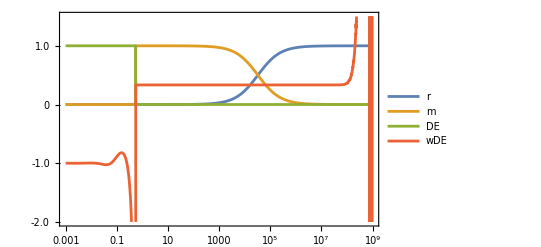

```mathematica
Plot[{(Ωr[-Log[x]]/.Sol),(Ωm[-Log[x]]/.Sol),(ΩDE[-Log[x]]/.Sol),(wDE[-Log[x]]/.Sol)},{x,10^-3,10^9},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^9},{-2,1.5}},PlotLegends->{"r","m","DE","wDE"}]
```

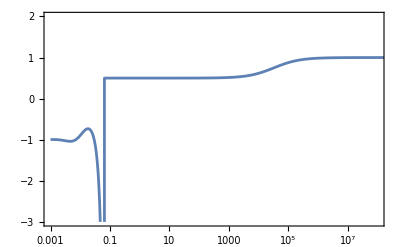

```mathematica
Plot[(-1+ϵ[-Log[x]]/.Sol),{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{MaTeX["\\epsilon"]},PlotRange->{{10^-3,10^8},{-3,2}}]
```

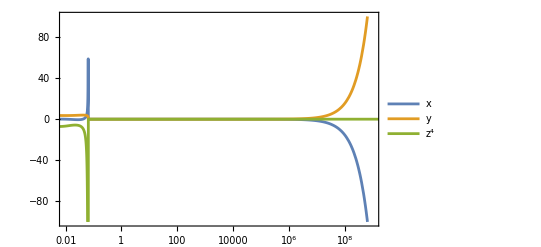

```mathematica
Plot[{(x[-Log[x]]/.Sol),(y[-Log[x]]/.Sol),(Z[-Log[x]]/.Sol)},{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-2,10^9},{-100,100}},PlotLegends->{"x","y","z^4"}]
```

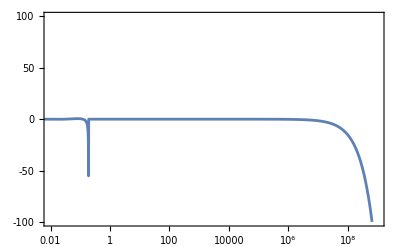

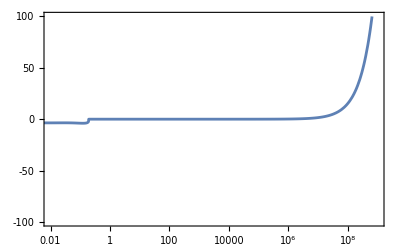

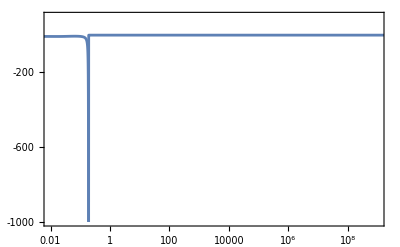

```mathematica
Plot[{(x[-Log[x]]/.Sol)},{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-2,10^9},{-100,100}}]
Plot[{(y[-Log[x]]/.Sol)},{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-2,10^9},{-100,100}}]
Plot[{(Z[-Log[x]]/.Sol)},{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-2,10^9},{-1000,100}}]
```

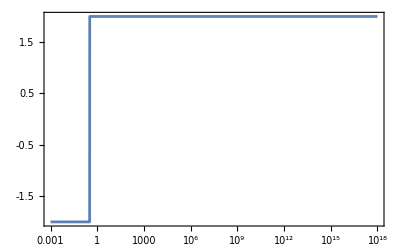

```mathematica
Plot[{(2Sign@Z[-Log[x]]/.Sol)},{x,10^-3,10^18},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"}]
```

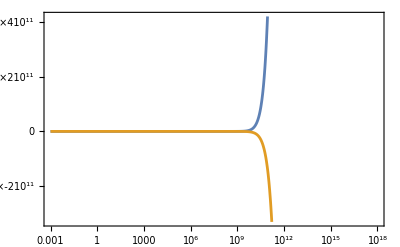

```mathematica
Plot[{((x[-Log[x]]+y[-Log[x]])^2(1-4c2 y[-Log[x]]^2)/.Sol),(x[-Log[x]] y[-Log[x]]^3(c1-c2)+2Z[-Log[x]])/.Sol},{x,10^-3,10^18},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"}]
```

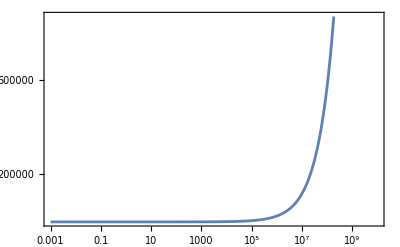

```mathematica
Plot[(Ωm[-Log[x]]/.Sol),{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{MaTeX["\\epsilon"]}]
```